```mathematica
Needs["PlotLegends`"]
```

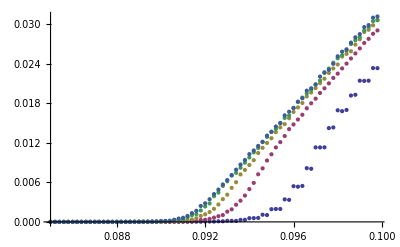

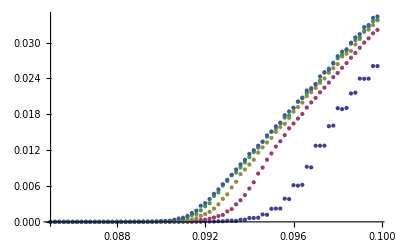

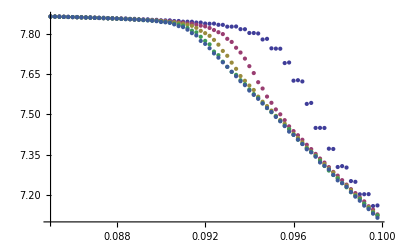

```mathematica
v="8";
p="0.1";

g2k1R=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/GapD-l2k-v"<>v<>"-p0.1-low.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v2k1R=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/VelD-l2k-v"<>v<>"-p0.1-low.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av2k1R=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/AveVel-l2k-v"<>v<>"-p0.1-low.txt",{Number,Number,Number,Number}];


g5k1R=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/GapD-l5k-v"<>v<>"-p0.1-low.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v5k1R=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/VelD-l5k-v"<>v<>"-p0.1-low.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av5k1R=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/AveVel-l5k-v"<>v<>"-p0.1-low.txt",{Number,Number,Number,Number}];

g10k1R=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/GapD-l10k-v"<>v<>"-p0.1-low.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v10k1R=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/VelD-l10k-v"<>v<>"-p0.1-low.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av10k1R=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/AveVel-l10k-v"<>v<>"-p0.1-low.txt",{Number,Number,Number,Number}];
g20k1R=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/GapD-l20k-v"<>v<>"-p0.1-low.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v20k1R=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/VelD-l20k-v"<>v<>"-p0.1-low.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av20k1R=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/AveVel-l20k-v"<>v<>"-p0.1-low.txt",{Number,Number,Number,Number}];

g30k1R=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/GapD-l30k-v"<>v<>"-p0.1-low.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v30k1R=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/VelD-l30k-v"<>v<>"-p0.1-low.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av30k1R=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/AveVel-l30k-v"<>v<>"-p0.1-low.txt",{Number,Number,Number,Number}];

ngap="0";
nvel="0";
jj=StringToStream[ngap];
ng= Read[jj,Number];
ii=StringToStream[nvel];
nv= Read[ii,Number];
ClearAll[d0,z,α];
d0=0.0674;
z=0.65;
α=0.65;

gap2v8R=Table[{g2k1R[[All,1]][[j]],Sum[g2k1R[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g2k1R]}];
vel2v8R=Table[{v2k1R[[All,1]][[j]],Sum[v2k1R[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v2k1R]}];
avel2v8R=Table[{av2k1R[[All,1]][[j]],av2k1R[[All,2]][[j]]},{j,1,Length[av2k1R]}];

gap5v8R=Table[{g5k1R[[All,1]][[j]],Sum[g5k1R[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g5k1R]}];
vel5v8R=Table[{v5k1R[[All,1]][[j]],Sum[v5k1R[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v5k1R]}];
avel5v8R=Table[{av5k1R[[All,1]][[j]],av5k1R[[All,2]][[j]]},{j,1,Length[av5k1R]}];


gap10v8R=Table[{g10k1R[[All,1]][[j]],Sum[g10k1R[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g10k1R]}];
vel10v8R=Table[{v10k1R[[All,1]][[j]],Sum[v10k1R[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v10k1R]}];
avel10v8R=Table[{av10k1R[[All,1]][[j]],av10k1R[[All,2]][[j]]},{j,1,Length[av10k1R]}];

gap20v8R=Table[{g20k1R[[All,1]][[j]],Sum[g20k1R[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g20k1R]}];
vel20v8R=Table[{v20k1R[[All,1]][[j]],Sum[v20k1R[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v20k1R]}];
avel20v8R=Table[{av20k1R[[All,1]][[j]],av20k1R[[All,2]][[j]]},{j,1,Length[av20k1R]}];

gap30v8R=Table[{g30k1R[[All,1]][[j]],Sum[g30k1R[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g30k1R]}];
vel30v8R=Table[{v30k1R[[All,1]][[j]],Sum[v30k1R[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v30k1R]}];
avel30v8R=Table[{av30k1R[[All,1]][[j]],av30k1R[[All,2]][[j]]},{j,1,Length[av30k1R]}];


ListPlot[{gap2v8R,gap5v8R,gap10v8R,gap20v8R,gap30v8R},PlotRange->Full]
ListPlot[{vel2v8R,vel5v8R,vel10v8R,vel20v8R,vel30v8R},PlotRange->Full]
ListPlot[{avel2v8R,avel5v8R,avel10v8R,avel20v8R,avel30v8R}]
```

```mathematica
************************************************************
```

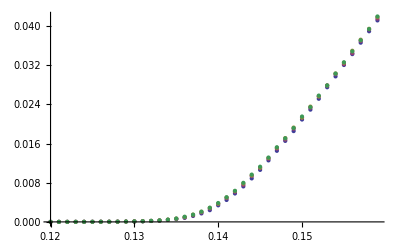

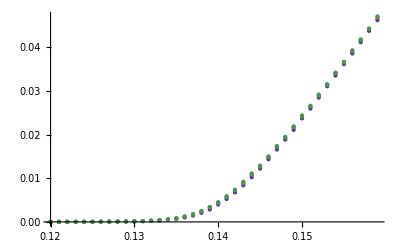

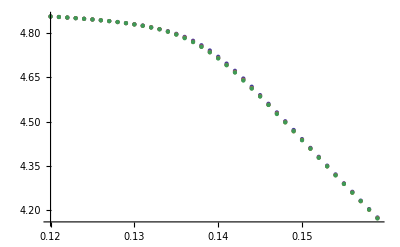

```mathematica
v="5";
p="0.1";

g5k1R=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/GapD-l5k-v"<>v<>"-p0.1-low.txt",{Number,Number,Number,Number,Number,Number,Number}];
v5k1R=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/VelD-l5k-v"<>v<>"-p0.1-low.txt",{Number,Number,Number,Number,Number,Number,Number}];
av5k1R=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/AveVel-l5k-v"<>v<>"-p0.1-low.txt",{Number,Number,Number,Number}];

g10k1R=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/GapD-l10k-v"<>v<>"-p0.1-low.txt",{Number,Number,Number,Number,Number,Number,Number}];
v10k1R=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/VelD-l10k-v"<>v<>"-p0.1-low.txt",{Number,Number,Number,Number,Number,Number,Number}];
av10k1R=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/AveVel-l10k-v"<>v<>"-p0.1-low.txt",{Number,Number,Number,Number}];
g20k1R=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/GapD-l20k-v"<>v<>"-p0.1-low.txt",{Number,Number,Number,Number,Number,Number,Number}];
v20k1R=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/VelD-l20k-v"<>v<>"-p0.1-low.txt",{Number,Number,Number,Number,Number,Number,Number}];
av20k1R=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/AveVel-l20k-v"<>v<>"-p0.1-low.txt",{Number,Number,Number,Number}];

g30k1R=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/GapD-l30k-v"<>v<>"-p0.1-low.txt",{Number,Number,Number,Number,Number,Number,Number}];
v30k1R=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/VelD-l30k-v"<>v<>"-p0.1-low.txt",{Number,Number,Number,Number,Number,Number,Number}];
av30k1R=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/AveVel-l30k-v"<>v<>"-p0.1-low.txt",{Number,Number,Number,Number}];

ngap="0";
nvel="0";
jj=StringToStream[ngap];
ng= Read[jj,Number];
ii=StringToStream[nvel];
nv= Read[ii,Number];
ClearAll[d0,z,α];
d0=0.0674;
z=0.65;
α=0.65;

gap5v5R=Table[{g5k1R[[All,1]][[j]],Sum[g5k1R[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g5k1R]}];
vel5v5R=Table[{v5k1R[[All,1]][[j]],Sum[v5k1R[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v5k1R]}];
avel5v5R=Table[{av5k1R[[All,1]][[j]],av5k1R[[All,2]][[j]]},{j,1,Length[av5k1R]}];

gap10v5R=Table[{g10k1R[[All,1]][[j]],Sum[g10k1R[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g10k1R]}];
vel10v5R=Table[{v10k1R[[All,1]][[j]],Sum[v10k1R[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v10k1R]}];
avel10v5R=Table[{av10k1R[[All,1]][[j]],av10k1R[[All,2]][[j]]},{j,1,Length[av10k1R]}];

gap20v5R=Table[{g20k1R[[All,1]][[j]],Sum[g20k1R[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g20k1R]}];
vel20v5R=Table[{v20k1R[[All,1]][[j]],Sum[v20k1R[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v20k1R]}];
avel20v5R=Table[{av20k1R[[All,1]][[j]],av20k1R[[All,2]][[j]]},{j,1,Length[av20k1R]}];

gap30v5R=Table[{g30k1R[[All,1]][[j]],Sum[g30k1R[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g30k1R]}];
vel30v5R=Table[{v30k1R[[All,1]][[j]],Sum[v30k1R[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v30k1R]}];
avel30v5R=Table[{av30k1R[[All,1]][[j]],av30k1R[[All,2]][[j]]},{j,1,Length[av30k1R]}];


ListPlot[{gap5v5R,gap10v5R,gap20v5R,gap30v5R},PlotRange->Full]
ListPlot[{vel5v5R,vel10v5R,vel20v5R,vel30v5R},PlotRange->Full]
ListPlot[{avel5v5R,avel10v5R,avel20v5R,avel30v5R}]
```

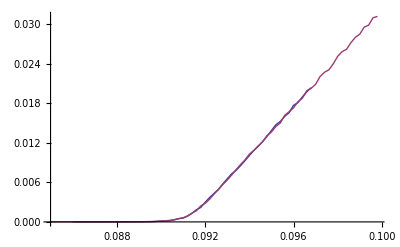

```mathematica
ListLinePlot[{gap30v8,gap30v8R}]
```

```mathematica
**************************************************************
```

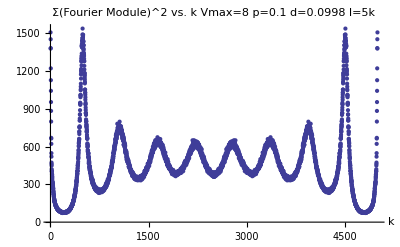

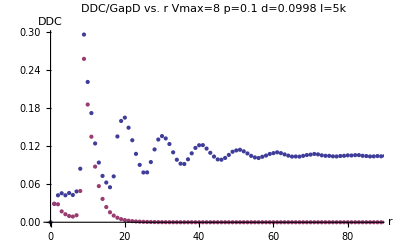

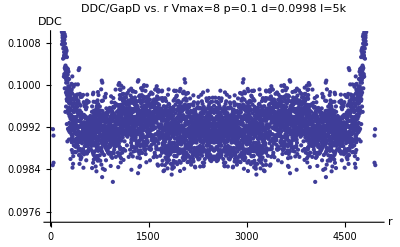

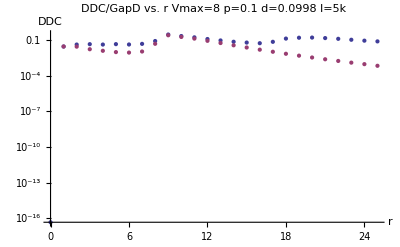

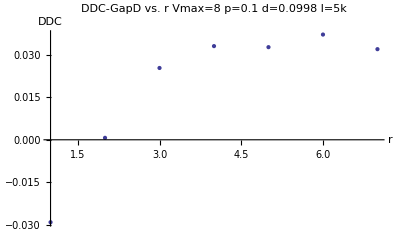

```mathematica
d="0.0998";
l="5";
v="8";
p="0.1";
fourierR=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/Fourier1D-d"<>d<>"-l"<>l<>"k-v"<>v<>"-p"<>p<>".txt",{Number,Number}];
ddcR=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/DDC-d"<>d<>"-l"<>l<>"k-v"<>v<>"-p"<>p<>".txt",{Number,Number}];
gfR=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/GapDFull-d"<>d<>"-l"<>l<>"k-v"<>v<>"-p"<>p<>".txt",{Number,Number}];
jj=StringToStream[v];
vmax= Read[jj,Number];
difR=Table[{i,ddcR[[All,2]][[i]]-gfR[[All,2]][[i]]},{i,1,vmax-1}];
ListPlot[fourierR,PlotLabel->"Σ(Fourier Module)^2 vs. k Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",AxesLabel->{"k"," "},PlotRange->Full]
ListPlot[{ddcR,gfR},PlotLabel->"DDC/GapD vs. r Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",AxesLabel->{"r","DDC"},PlotRange->{{0,88},Full},PlotLegend->{"DDC","Gap D."},LegendPosition->{1.1,-0.4},LegendSize->{0.4,0.6},LegendShadow->None]
ListPlot[{ddcR,gfR},PlotLabel->"DDC/GapD vs. r Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",AxesLabel->{"r","DDC"},PlotRange->{Full}]
ListLogPlot[{ddcR,gfR},PlotLabel->"DDC/GapD vs. r Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",AxesLabel->{"r","DDC"},PlotRange->{{0,25},Full}]
ListPlot[difR,PlotLabel->"DDC-GapD vs. r Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",AxesLabel->{"r","DDC"}]
```

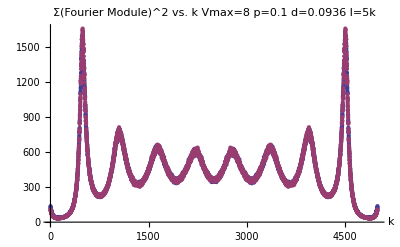

```mathematica
ListPlot[{fourierR,fourier},PlotLabel->"Σ(Fourier Module)^2 vs. k Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",AxesLabel->{"k"," "},PlotRange->Full,PlotLegend->{"Random-GSL","Random-C++"},LegendPosition->{1.1,-0.4},LegendSize->{0.4,0.6},LegendShadow->None]
```

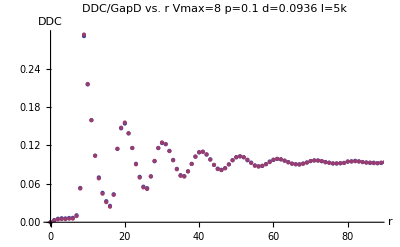

```mathematica
ListPlot[{ddcR,ddc},PlotLabel->"DDC/GapD vs. r Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",AxesLabel->{"r","DDC"},PlotRange->{{0,88},Full},PlotLegend->{"Random-GSL","Random-C++"},LegendPosition->{1.1,-0.4},LegendSize->{0.4,0.6},LegendShadow->None]
```